# TAYLOR EXPANSION

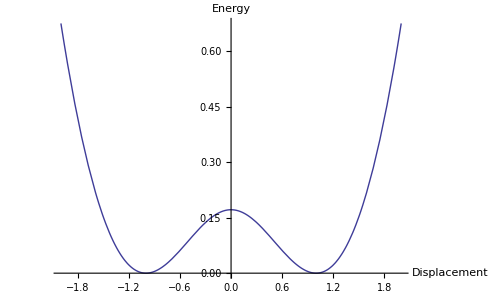

```mathematica
δ = 2;
l = 1;
k = 1;
l2 = 6;
L = √((δ/2)^2+l^2);
Lp[u_] := √(L^2- 2l u + u^2);
X[u_] := Lp[u]-L;
En[u_]:=k X[u]^2
F[u_] := -En'[u];
A = -F[-l/2];
G[u_]:= -((2 √((δ/2)^2+l^2))/(√(4(δ/2)^2+l^2))-1)Sin[π u];
Plot[{En[v+1],EnT[v]},{v,-2l,2l}, AxesLabel-> {"Displacement","Energy"}]
Entri[u_] := En[l2-√(l2^2-u^2)]
```

```mathematica
EnT[x_]=Collect[Series[F[x],{x,0,3}],x]
```

-x+(3 x^2)/4+(3 x^3)/8

```mathematica
-v+(3 v^2)/4+(3 v^3)/8
```

11.4568

```mathematica
EnT'[v]
```

0

```mathematica
-x+(3 x^2)/4+(3 x^3)/8
```

-x+(3 x^2)/4+(3 x^3)/8

```mathematica
Force[u_]:=-F[u-2]
```

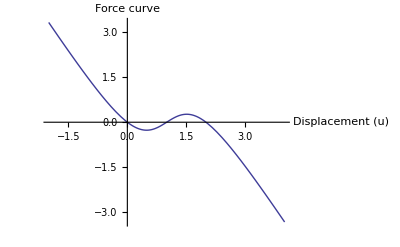

```mathematica
Plot[F[u],{u,-2,4}, AxesLabel-> {"Displacement (u)", "Force curve"}]
```

```mathematica
PlotLegends->Placed[{"Actual Force curve","Cubic(Medium u^-)","Linear (Small u^-)" },{Right,Top}]
```

PlotLegends→Placed[{Actual Force curve,Cubic(Medium u^-),Linear (Small u^-)},{Right,Top}]

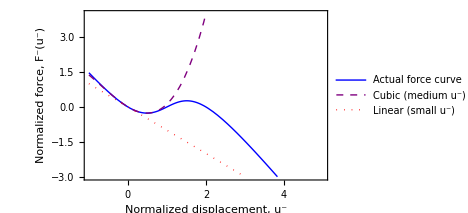

```mathematica
styles={Directive[Blue],Directive[Purple,Dashed],Directive[Red,Dotted,Thick]};plot=Plot[{F[u],EnT[u],-u} ,{u,-1,5},AspectRatio->1/GoldenRatio,PlotRange-> {-3,4}, FrameLabel-> {"Normalized displacement, u^-", "Normalized force, F^-(u^-)"}, AspectRatio-> 0.75, PlotStyle->{styles[[1]],styles[[2]],styles[[3]]},Frame->True,PlotLegends->Placed[LineLegend[{styles[[1]],styles[[2]],styles[[3]]},{"Actual force curve","Cubic (medium u^-)","Linear (small u^-)" }],{Right,Top}],BaseStyle->{FontFamily->"Times",14}]
```

```mathematica
LineLegend[{Dashed,styles[[2]],Dashed},{"Actual force curve","Cubic (medium u^-)","Linear (small u^-)" }]
```

```mathematica
Export["regimes.pdf",plot]
```

regimes.pdf

Show::gcomb: Could not combine the graphics objects in ….

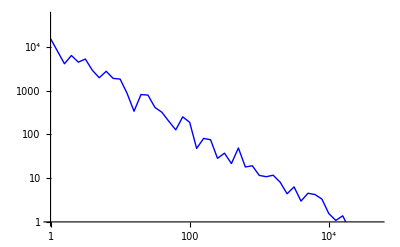
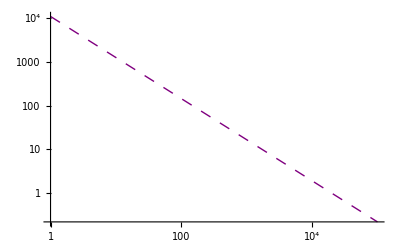
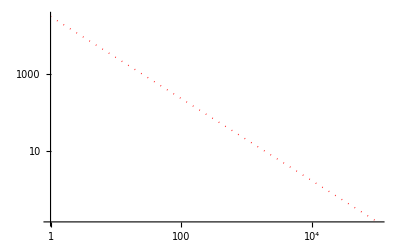
Show[-Graphics-,-Graphics-,-Graphics-,simpleLegend[{{data,Directive[RGBColor[0,0,1]]},{eq1,Directive[RGBColor[0.5,0,0.5],Dashing[0.02]]},{eq2,Directive[RGBColor[1,0,0],Dashing[{0,Small}],Thickness[Large]]}},{Right,Top}]]

```mathematica
labels={"data","eq1","eq2"};
styles={Directive[Blue],Directive[Purple,Dashing[0.02]],Directive[Red,Dotted,Thick]};

depth4=Table[{x,(11024 x^(-0.94232))*RandomReal[{0.4,1.6}]}/.x->10^n,{n,0,5,0.1}];

plot=ListLogLogPlot[Sort[depth4],PlotRange->{{1,50000},{1,50000}},Joined->True,PlotStyle->styles[[1]],BaseStyle->{FontSize->14}];

line=LogLogPlot[11024 x^(-0.94232),{x,1,100000},PlotStyle->styles[[2]]];
line2=LogLogPlot[31862 x^(-1.07076),{x,1,100000},PlotStyle->styles[[3]]];

Show[plot,line,line2,simpleLegend[Thread@{labels,styles},{Right,Top}]]
```

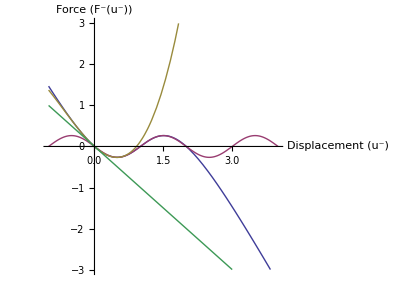

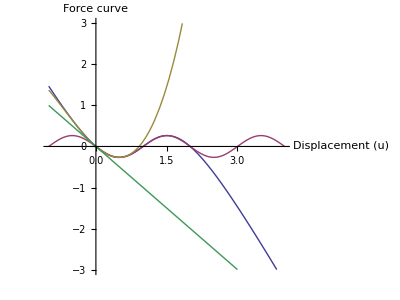

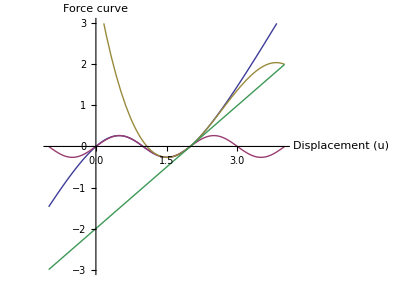

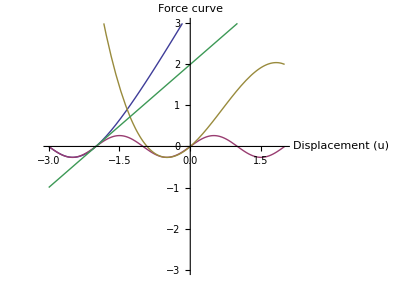

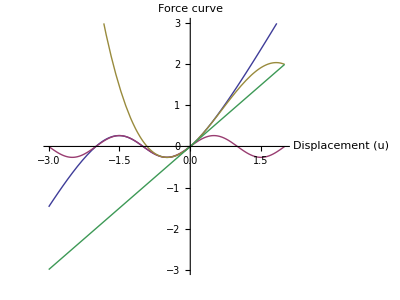

```mathematica
FullSimplify[∫(ⅆ x)/(√EnT[x])]
```

(x √(32+16 x-6 x^2) (Log[x]-Log[4+x+√(16+8 x-3 x^2)]))/(√(-(-4+x) x^2 (4+3 x)))

```mathematica
FullSimplify[D[(Log[x]-Log[4+x+√(16+8 x-3 x^2)]),x]]
```

```mathematica
Solve[z== Log[x]-Log[4+x+√(16+8 x-3 x^2)],x]
```

{{x→(8 ⅇ^z)/(1-2 ⅇ^z+4 ⅇ^(2 z))}}

```mathematica
Sol[z_] := (8 ⅇ^z)/(1-2 ⅇ^z+4 ⅇ^(2 z))
```

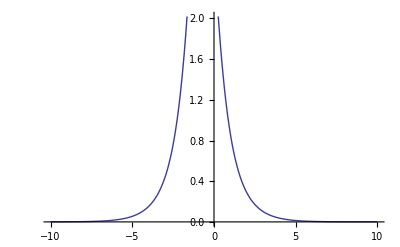

```mathematica
Plot[Sol[z],{z,-10,10}]
```

```mathematica
pde = D[D[ϕ[x,t],t],t]-D[D[ϕ[x,t],t],t] + ϕ[x,t]+(3 ϕ[x,t]^2)/4-(3 ϕ[x,t]^3)/8==0;
```

```mathematica
soln = DSolve[pde,ϕ[x,t],{x,t}]
```

{{ϕ[x,t]→0},{ϕ[x,t]→1/3 (3-√33)},{ϕ[x,t]→1/3 (3+√33)}}

```mathematica
Needs["PlotLegends`"]
Plot[{Force[u],Force[0.5]Sin[π u]},{u,0,2},PlotRange-> {-0.3,0.3}, AxesLabel-> {"Displacement (u)", "Force curve"}, AspectRatio-> 0.75, PlotLegends-> {"Actual Force Curve","Sine curve (Large u)" }]
```

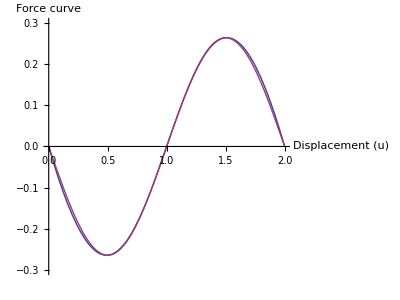

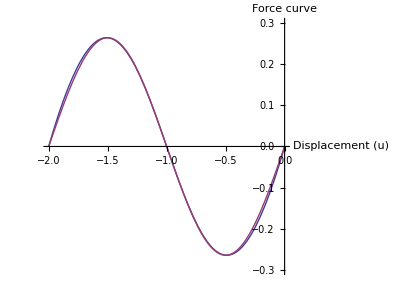

```mathematica
Needs["PlotLegends`"]
Plot[{Force[u],EnT[u]},{u,-0.6,0.6},PlotRange-> {-1,1}, AxesLabel-> {"Displacement (u)", "Force curve"}, AspectRatio-> 1, PlotLegends-> {"Actual Force Curve","3rd Order Cubic Taylor" }]
```

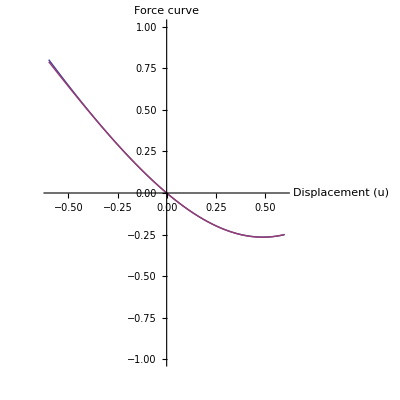

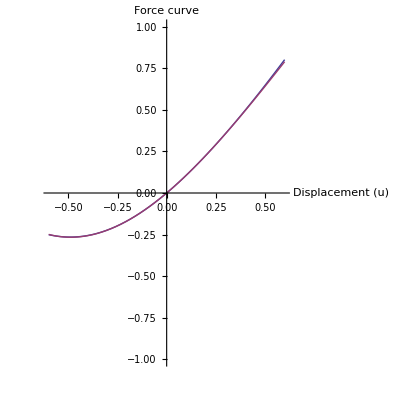

```mathematica
Needs["PlotLegends`"]
Plot[{Force[u],-u},{u,-0.05,0.05}, AxesLabel-> {"Displacement (u)", "Force curve"}, AspectRatio-> 0.75, PlotLegend-> {"Actual Force Curve","1st Order Linear Taylor" }]
```

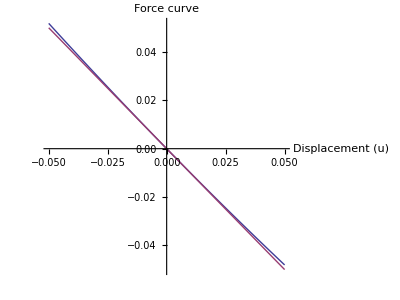

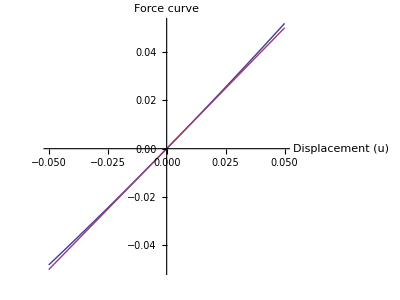

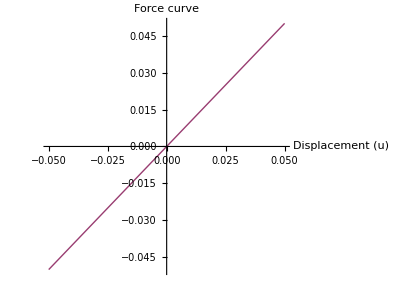

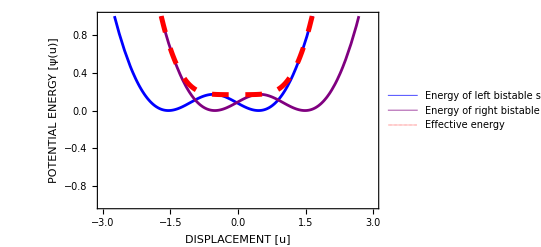

```mathematica
a=1.03;
Aplot=Plot[{En[u+3a/2],En[u+3a/2-a], En[u+3a/2]+En[u+3a/2-a]},{u,-3,3},PlotRange-> {-1,1},Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]],Directive[Purple,Thickness[0.005]],Directive[Red,Thickness[0.009],Dashing[0.03]],Directive[Black,Thickness[0.005],Dashing[0.03]]}, FrameLabel->{"DISPLACEMENT [u]","POTENTIAL ENERGY [ψ(u)]"},PlotLegends->Placed[{"Energy of left bistable spring","Energy of right bistable spring","Effective energy","Effective energy of the structure"},{Left,Bottom}]]
```

```mathematica
Export["Energy.PDF",Aplot];
```

```mathematica
Import["energy.pdf"]
```

{-Graphics-}

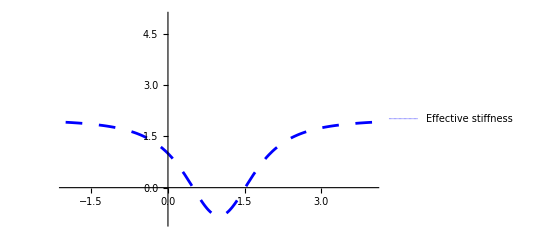

```mathematica
Bplot=Plot[En''[u],{u,-2,4},PlotRange-> {-1,5},PlotStyle->{Directive[Blue,Thickness[0.005],Dashing[0.03]]}, FrameLabel->{"DISPLACEMENT [u]"," EFFECTIVE STIFFNESS [K(u)]"},PlotLegends->Placed[{"Effective stiffness"},{Left,Top}]]
```

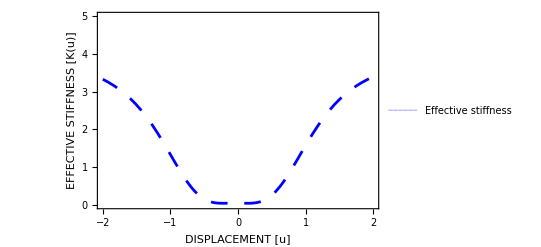

```mathematica
Export["stiffness.pdf",Bplot]
```

stiffness.pdf

```mathematica
En''[0+3a/2]+En''[0+3a/2-a]
```

0.0727389

```mathematica
Ftri[u_] := Entri'[u];
```

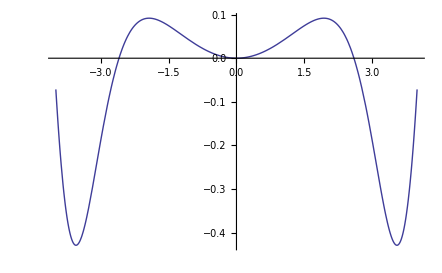

```mathematica
Plot[Ftri'[u],{u,-4,4}]
```

```mathematica
ψ[u_]=(√((1-u)^2+d^2)-√(1+d^2))^2;
Integrate[1/(√(ψ[u+uo]-u ψ'[uo])),u]
```

∫1/(√((-√(1+d^2)+√(d^2+(1-u-uo)^2))^2+(2 u (-√(1+d^2)+√(d^2+(1-uo)^2)) (1-uo))/(√(d^2+(1-uo)^2))))ⅆu

```mathematica
Expand[ψ[u+uo]-u ψ'[uo]]
```

```mathematica
Integrate[1/(3.04-2 √2 √(1+(0.19999999999999996-u)^2)-0.554700196225229 u+u^2),u]
```

∫1/(3.04-2 √2 √(1+(0.2-u)^2)-0.5547 u+u^2)ⅆu

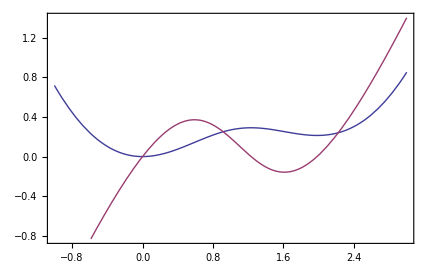

```mathematica
uo=-0.1;
d=1;
Plot[{ψ[u+uo]-u ψ'[uo]-ψ[uo],ψ'[u+uo]-ψ'[uo]},{u,-1,3},Frame->True]
```

```mathematica
Integrate[1/(√(ψ[u]u1-ψ[u1]u)),u]
```

∫1/(√(-u (-√2+√(1+(1-u1)^2))^2+(-√2+√(1+(1-u)^2))^2 u1))ⅆu